## Section 1 - Numerical solution of Reaction-Diffusion with a Theta-like rates - 3 species out of equilibrium

### Preliminary code

```mathematica
vecp={};
vece={};
nn=3;
t0=1;
de1=RandomReal[2,{nn,nn}];
de=(de1+Transpose[de1])/2;
en={1+Tanh[2 (x-3)],1.3+1.3Tanh[2 (x-3)],2+2Tanh[2 (x-3)]};
kvec=Table[Exp[-en[[i]]+de[[i,j]]] 1,{i,1,nn},{j,1,nn}]
For[i=1,i≤nn,i++,
kvec[[i,i]]=0;
];
sys=Quiet[Table[Sum[kvec[[j,i]] p[[j]][x]-kvec[[i,j]] p[[i]][x]+KroneckerDelta[j,i] D[p[[i]][x],{x,2}],{j,1,nn}]==0,{i,1,nn}]];
psol=Quiet[Table[p[[i]],{i,1,nn}]]/.Quiet[Flatten[NDSolve[Flatten[Join[sys,Table[p[[i]]'[0]==0,{i,1,nn}],Table[p[[i]]'[5]==0,{i,1,nn}]]],Table[p[[i]],{i,1,nn}],{x,0,5}]]];
ptot[xx_]:=Sum[psol[[i]][xx],{i,1,nn}];
```

{{ⅇ^(-0.323147-Tanh[2 (-3+x)]),ⅇ^(0.0726273-Tanh[2 (-3+x)]),ⅇ^(-0.0884193-Tanh[2 (-3+x)])},{ⅇ^(-0.227373-1.3 Tanh[2 (-3+x)]),ⅇ^(-0.966759-1.3 Tanh[2 (-3+x)]),ⅇ^(-0.557224-1.3 Tanh[2 (-3+x)])},{ⅇ^(-1.08842-2 Tanh[2 (-3+x)]),ⅇ^(-1.25722-2 Tanh[2 (-3+x)]),ⅇ^(-1.37774-2 Tanh[2 (-3+x)])}}

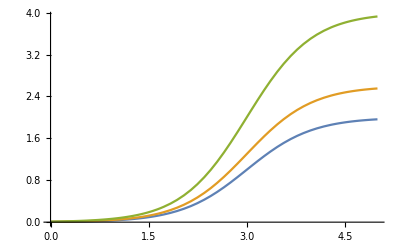

```mathematica
Plot[{en[[1]],en[[2]],en[[3]]},{x,0,5},PlotRange->All]
```

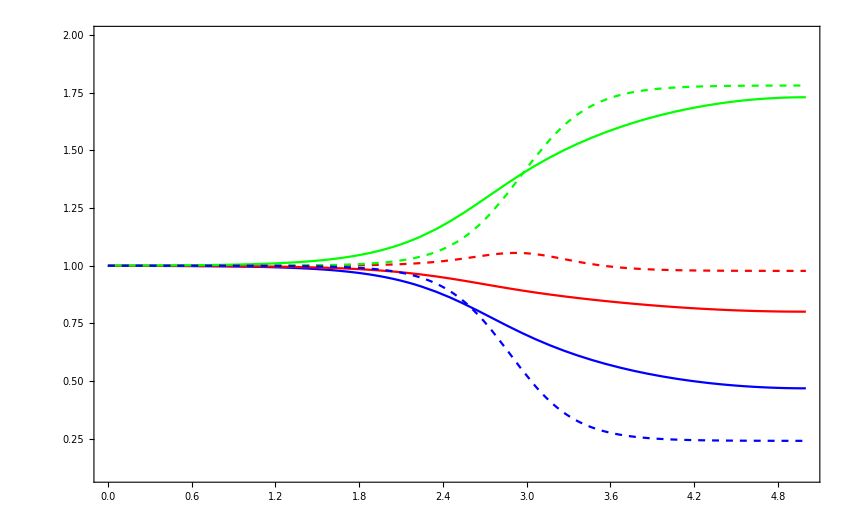

```mathematica
Plot[{psol[[1]][x],psol[[2]][x],psol[[3]][x],Exp[-en[[2]]]/(Exp[-en[[2]]]+Exp[-en[[3]]]+Exp[-en[[1]]]) ptot[x],Exp[-en[[1]]]/(Exp[-en[[2]]]+Exp[-en[[3]]]+Exp[-en[[1]]]) ptot[x],Exp[-en[[3]]]/(Exp[-en[[2]]]+Exp[-en[[3]]]+Exp[-en[[1]]]) ptot[x]},{x,0,5},PlotStyle->{Blue,Red,Green,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},PlotRange->{{0,5},{0.1,2}},Frame->True]
```

### Equilibrium solution Theta Heaviside

{{ⅇ^(1.80707-HeavisideTheta[-2+x]),ⅇ^(1.14056-1.3 HeavisideTheta[-2+x]),ⅇ^(0.975065-2 HeavisideTheta[-2+x])},{ⅇ^(1.14056-HeavisideTheta[-2+x]),ⅇ^(0.722441-1.3 HeavisideTheta[-2+x]),ⅇ^(0.867395-2 HeavisideTheta[-2+x])},{ⅇ^(0.975065-HeavisideTheta[-2+x]),ⅇ^(0.867395-1.3 HeavisideTheta[-2+x]),ⅇ^(0.668779-2 HeavisideTheta[-2+x])}}

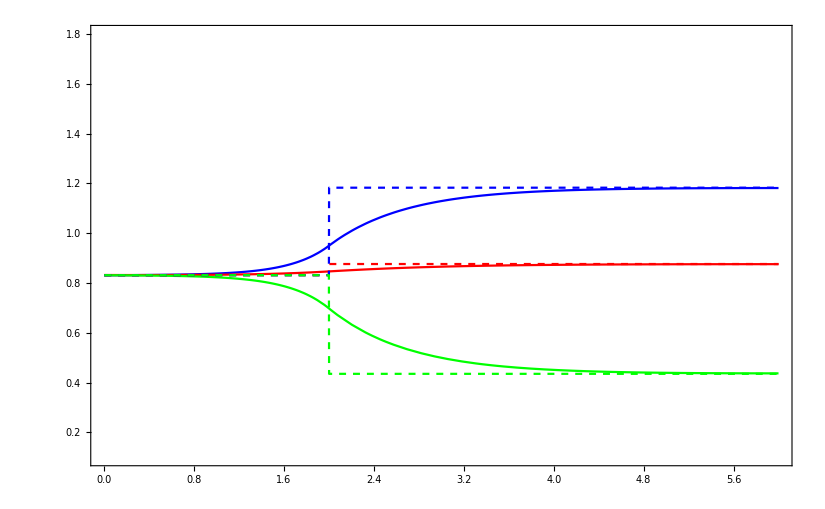

```mathematica
vecp={};
vece={};
nn=3;
t0=1;
de1=RandomReal[2,{nn,nn}];
de=(de1+Transpose[de1])/2;
en={1HeavisideTheta[x-2],1.3HeavisideTheta[x-2],2HeavisideTheta[x-2]};
kvec=Table[Exp[-en[[j]]+de[[i,j]]] 1,{i,1,nn},{j,1,nn}]
For[i=1,i≤nn,i++,
kvec[[i,i]]=0;
];
kvec[[1,2]]=kvec[[1,2]] Exp[0];
sys=Quiet[Table[Sum[kvec[[j,i]] p[[j]][x]-kvec[[i,j]] p[[i]][x]+KroneckerDelta[j,i] D[p[[i]][x],{x,2}],{j,1,nn}]==0,{i,1,nn}]];
psoleq=Quiet[Table[p[[i]],{i,1,nn}]]/.Quiet[Flatten[NDSolve[Flatten[Join[sys,Table[p[[i]]'[0]==0,{i,1,nn}],Table[p[[i]]'[6]==0,{i,1,nn}]]],Table[p[[i]],{i,1,nn}],{x,0,6}]]];
ptoteq[xx_]:=Sum[psoleq[[i]][xx],{i,1,nn}];
Plot[{psoleq[[1]][x],psoleq[[2]][x],psoleq[[3]][x],((kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x],((kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x],((kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x]},{x,0,6},PlotStyle->{Blue,Red,Green,{Red,Dashed},{Blue,Dashed},{Green,Dashed}},PlotRange->{{0,6},{0.1,1.8}},Frame->True]
```

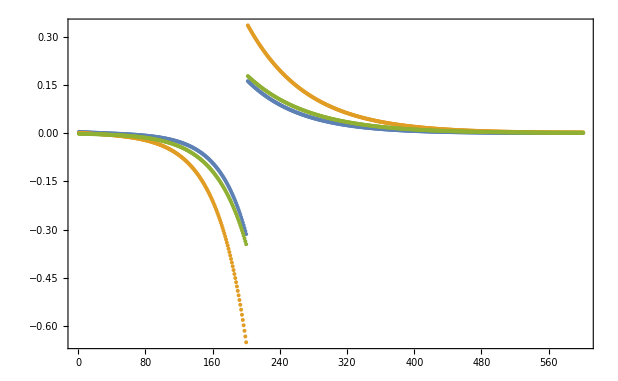

```mathematica
chemicalfluxes=Flatten[Table[kvec[[j,i]] psoleq[[j]][x]-kvec[[i,j]] psoleq[[i]][x],{i,1,nn},{j,i+1,nn}]];
ListPlot[{Table[chemicalfluxes[[1]]/.x->xx,{xx,0,6,0.01}],Table[chemicalfluxes[[2]]/.x->xx,{xx,0,6,0.01}],Table[chemicalfluxes[[3]]/.x->xx,{xx,0,6,0.01}]},PlotRange->All,Frame->True]
```

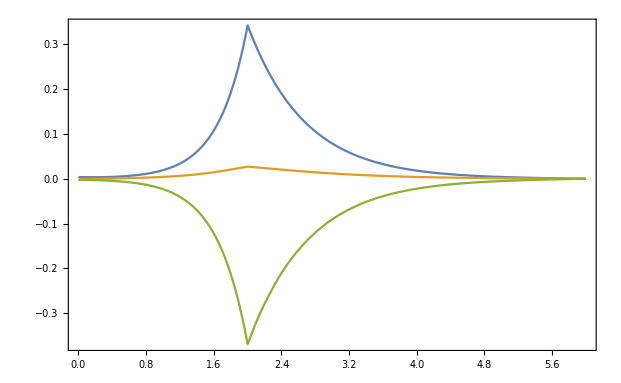

```mathematica
spatialfluxes=Table[D[psoleq[[j]][x],x],{j,1,nn}];
Plot[{spatialfluxes[[1]]/.x->xx,spatialfluxes[[2]]/.x->xx,spatialfluxes[[3]]/.x->xx},{xx,0,6},PlotRange->All,Frame->True]
```

### Nonequilibrium solution Theta Heaviside

{{ⅇ^(0.566284-HeavisideTheta[-2+x]),ⅇ^(0.502303-1.3 HeavisideTheta[-2+x]),ⅇ^(0.444508-2 HeavisideTheta[-2+x])},{ⅇ^(0.502303-HeavisideTheta[-2+x]),ⅇ^(0.278806-1.3 HeavisideTheta[-2+x]),ⅇ^(1.45741-2 HeavisideTheta[-2+x])},{ⅇ^(0.444508-HeavisideTheta[-2+x]),ⅇ^(1.45741-1.3 HeavisideTheta[-2+x]),ⅇ^(1.30598-2 HeavisideTheta[-2+x])}}

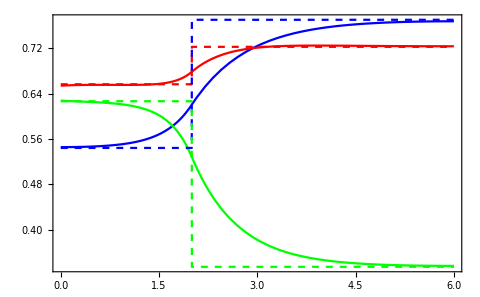

```mathematica
vecp={};
vece={};
nn=3;
t0=1;
de1=RandomReal[2,{nn,nn}];
de=(de1+Transpose[de1])/2;
en={1HeavisideTheta[x-2],1.3HeavisideTheta[x-2],2HeavisideTheta[x-2]};
kvecneq=Table[Exp[-en[[j]]+de[[i,j]]] 1,{i,1,nn},{j,1,nn}]
For[i=1,i≤nn,i++,
kvecneq[[i,i]]=0;
];
kvecneq[[1,2]]=kvecneq[[1,2]] Exp[0.3];
sys=Quiet[Table[Sum[kvecneq[[j,i]] p[[j]][x]-kvecneq[[i,j]] p[[i]][x]+KroneckerDelta[j,i] D[p[[i]][x],{x,2}],{j,1,nn}]==0,{i,1,nn}]];
psol=Quiet[Table[p[[i]],{i,1,nn}]]/.Quiet[Flatten[NDSolve[Flatten[Join[sys,Table[p[[i]]'[0]==0,{i,1,nn}],Table[p[[i]]'[6]==0,{i,1,nn}]]],Table[p[[i]],{i,1,nn}],{x,0,6}]]];
ptot[xx_]:=Sum[psol[[i]][xx],{i,1,nn}];
Plot[{psol[[1]][x],psol[[2]][x],psol[[3]][x],((kvecneq[[1,2]] kvecneq[[3,2]]+kvecneq[[1,3]] kvecneq[[3,2]]+kvecneq[[3,1]] kvecneq[[1,2]])/(kvecneq[[1,2]] kvecneq[[3,2]]+kvecneq[[1,3]] kvecneq[[3,2]]+kvecneq[[3,1]] kvecneq[[1,2]]+kvecneq[[2,1]] kvecneq[[3,1]]+kvecneq[[2,3]] kvecneq[[3,1]]+kvecneq[[3,2]] kvecneq[[2,1]]+kvecneq[[1,3]]kvecneq[[2,3]]+kvecneq[[1,2]]kvecneq[[2,3]]+kvecneq[[2,1]]kvecneq[[1,3]])) ptot[x],((kvecneq[[2,1]] kvecneq[[3,1]]+kvecneq[[2,3]] kvecneq[[3,1]]+kvecneq[[3,2]] kvecneq[[2,1]])/(kvecneq[[1,2]] kvecneq[[3,2]]+kvecneq[[1,3]] kvecneq[[3,2]]+kvecneq[[3,1]] kvecneq[[1,2]]+kvecneq[[2,1]] kvecneq[[3,1]]+kvecneq[[2,3]] kvecneq[[3,1]]+kvecneq[[3,2]] kvecneq[[2,1]]+kvecneq[[1,3]]kvecneq[[2,3]]+kvecneq[[1,2]]kvecneq[[2,3]]+kvecneq[[2,1]]kvecneq[[1,3]])) ptot[x],((kvecneq[[1,3]]kvecneq[[2,3]]+kvecneq[[1,2]]kvecneq[[2,3]]+kvecneq[[2,1]]kvecneq[[1,3]])/(kvecneq[[1,2]] kvecneq[[3,2]]+kvecneq[[1,3]] kvecneq[[3,2]]+kvecneq[[3,1]] kvecneq[[1,2]]+kvecneq[[2,1]] kvecneq[[3,1]]+kvecneq[[2,3]] kvecneq[[3,1]]+kvecneq[[3,2]] kvecneq[[2,1]]+kvecneq[[1,3]]kvecneq[[2,3]]+kvecneq[[1,2]]kvecneq[[2,3]]+kvecneq[[2,1]]kvecneq[[1,3]])) ptot[x]},{x,0,6},PlotStyle->{Blue,Red,Green,{Red,Dashed},{Blue,Dashed},{Green,Dashed}},Frame->True]
```

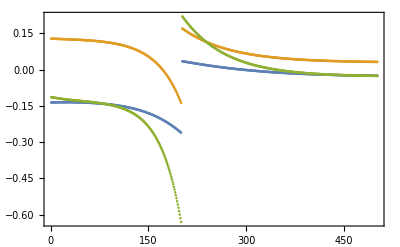

```mathematica
chemicalfluxesneq=Flatten[Table[kvecneq[[j,i]] psol[[j]][x]-kvecneq[[i,j]] psol[[i]][x],{i,1,nn},{j,i+1,nn}]];
ListPlot[{Table[chemicalfluxesneq[[1]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxesneq[[2]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxesneq[[3]]/.x->xx,{xx,0,5,0.01}]},PlotRange->All,Frame->True]
```

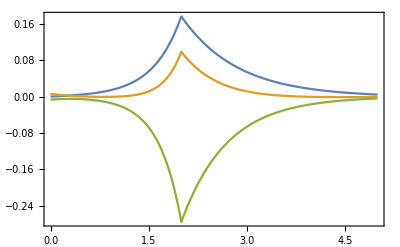

```mathematica
spatialfluxesneq=Table[D[psol[[j]][x],x],{j,1,nn}];
Plot[{spatialfluxesneq[[1]]/.x->xx,spatialfluxesneq[[2]]/.x->xx,spatialfluxesneq[[3]]/.x->xx},{xx,0,5},PlotRange->All,Frame->True]
```

### Equilibrium and nonequilibrium comparison

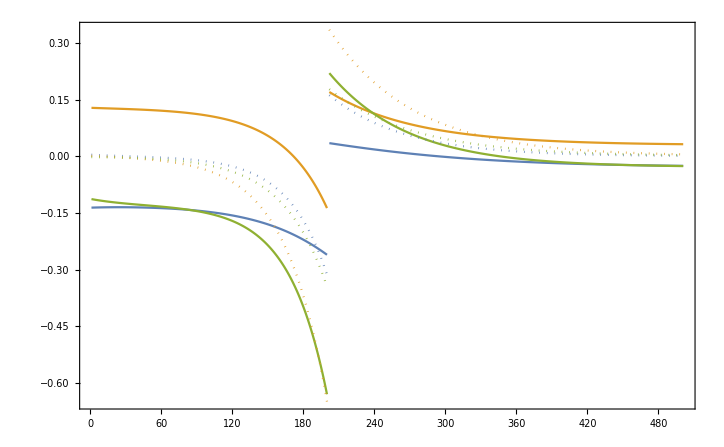

```mathematica
Show[ListPlot[{Table[chemicalfluxesneq[[1]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxesneq[[2]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxesneq[[3]]/.x->xx,{xx,0,5,0.01}]},PlotRange->All,Frame->True,Joined->True],ListPlot[{Table[chemicalfluxes[[1]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxes[[2]]/.x->xx,{xx,0,5,0.01}],Table[chemicalfluxes[[3]]/.x->xx,{xx,0,5,0.01}]},PlotRange->All,Frame->True,Joined->True,PlotStyle->Dotted],PlotRange->All]
```

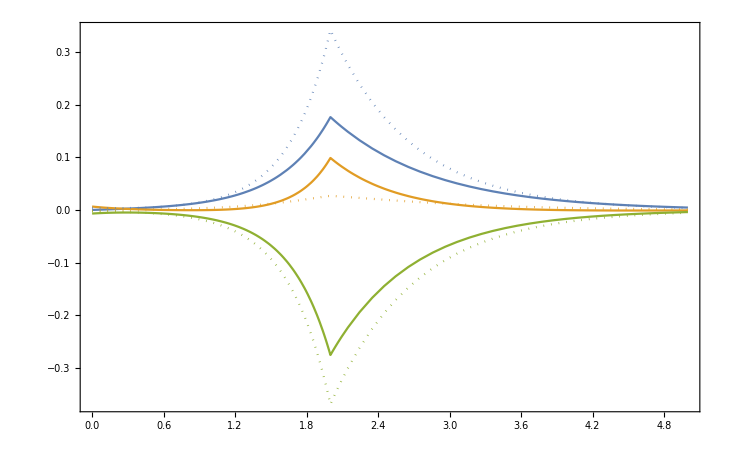

```mathematica
Show[Plot[{spatialfluxesneq[[1]]/.x->xx,spatialfluxesneq[[2]]/.x->xx,spatialfluxesneq[[3]]/.x->xx},{xx,0,5},PlotRange->All,Frame->True],Plot[{spatialfluxes[[1]]/.x->xx,spatialfluxes[[2]]/.x->xx,spatialfluxes[[3]]/.x->xx},{xx,0,5},PlotRange->All,Frame->True,PlotStyle->Dotted]]
```

```mathematica
VectorPlot[{If[rr<1,(D[gb[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(D[pB0[r]/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}],0},{rr,-0.1,4.2},{y,-1.2,1.2},VectorPoints->Table[{x,-1},{x,0,4,0.08}],PlotLegends->Automatic],VectorPlot[{0,If[r<1,(k1x ga[r]-km1x gb[r])/.sol/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},0]},{r,-0.1,4},{y,-1,1},VectorColorFunction->"AvocadoColors",PlotLegends->Automatic],VectorPlot[{0,If[r<1,0,(k1 pA0[r]-km1 pB0[r])/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}]},{r,1,4},{y,-1,1},VectorColorFunction->"DeepSeaColors",PlotLegends->Automatic]]
```

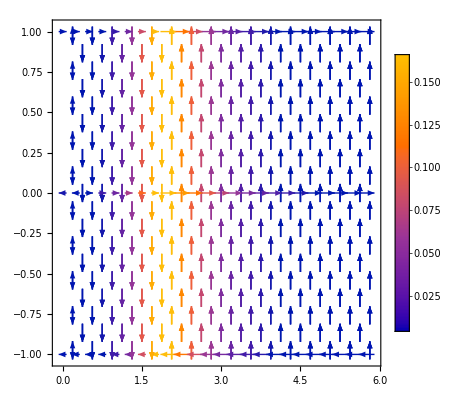

```mathematica
Show[VectorPlot[{spatialfluxes[[1]]/.x->xx,0},{xx,0,1.999},{y,-1.2,1.2},VectorPoints->Table[{x,1},{x,0,1.999,0.25}],PlotLegends->Automatic],VectorPlot[{spatialfluxes[[1]]/.x->xx,0},{xx,2.001,6},{y,-1.2,1.2},VectorPoints->Table[{x,1},{x,2.001,6,0.25}],PlotLegends->Automatic],VectorPlot[{spatialfluxes[[2]]/.x->xx,0},{xx,0,1.999},{y,-1.2,2.2},VectorPoints->Table[{x,0},{x,0,1.999,0.25}],PlotLegends->Automatic],VectorPlot[{spatialfluxes[[2]]/.x->xx,0},{xx,2.001,6},{y,-1.2,1.2},VectorPoints->Table[{x,0},{x,2.001,6,0.25}],PlotLegends->Automatic],VectorPlot[{spatialfluxes[[3]]/.x->xx,0},{xx,0,1.999},{y,-1.2,1.2},VectorPoints->Table[{x,-1},{x,0,1.999,0.25}],PlotLegends->Automatic],VectorPlot[{spatialfluxes[[3]]/.x->xx,0},{xx,2.001,6},{y,-1.2,1.2},VectorPoints->Table[{x,-1},{x,2.001,6,0.25}],PlotLegends->Automatic],VectorPlot[{0,chemicalfluxes[[1]]/.x->xx},{xx,0,6},{y,-1,1},PlotLegends->Automatic],VectorPlot[{0,chemicalfluxes[[2]]/.x->xx},{xx,0,6},{y,-1,1},PlotLegends->Automatic],VectorPlot[{0,chemicalfluxes[[3]]/.x->xx},{xx,0,6},{y,-1,1},PlotLegends->Automatic],PlotRange->All]
```

## Section 2 - Fast-reaction limit for Reaction-Diffusion with a potential interface

## Section 3 - Smoluchowski-like for Reaction-Diffusion with a sharp interface - 2 species chemostatted (non-eq)

```mathematica
pA0[r_]:=pAinf+b/r Exp[-Sqrt[k1+km1] r]
pB0[r_]:=pAinf k1/km1-b/r Exp[-Sqrt[k1+km1] r]
1/r^2 D[r^2 D[pA0[r],r],r]+km1 pB0[r]-k1 pA0[r]//FullSimplify
1/r^2 D[r^2 D[pB0[r],r],r]-km1 pB0[r]+k1 pA0[r]//FullSimplify
```

0

0

```mathematica
pA1[r_]:=ga[r]
pB1[r_]:=gb[r]
1/r^2 D[r^2 D[pA1[r],r],r]+km1x pB1[r]-k1x pA1[r]//FullSimplify
1/r^2 D[r^2 D[pB1[r],r],r]-km1x pB1[r]+k1x pA1[r]//FullSimplify
```

-k1x ga[r]+km1x gb[r]+(2 ga'[r])/r+ga''[r]

k1x ga[r]-km1x gb[r]+(2 gb'[r])/r+gb''[r]

```mathematica
sol=Flatten[DSolve[{-k1x ga[r]+km1x gb[r]+(2 ga'[r])/r+ga''[r]==0,k1x ga[r]-km1x gb[r]+(2 gb'[r])/r+gb''[r]==0,ga'[0]==0,gb'[0]==0,ga[1]==gaB,gb[1]==gbB},{ga[r],gb[r]},{r,0,1}]]
```

{ga[r]→(ⅇ^(-√(k1x+km1x) r) (ⅇ^(√(k1x+km1x) (1+2 r)) (gaB k1x-gbB km1x)+ⅇ^(√(k1x+km1x)) (-gaB k1x+gbB km1x)-ⅇ^(√(k1x+km1x) r) (gaB+gbB) km1x r+ⅇ^(√(k1x+km1x) (2+r)) (gaB+gbB) km1x r))/((-1+ⅇ^(2 √(k1x+km1x))) (k1x+km1x) r),gb[r]→(ⅇ^(-√(k1x+km1x) r) (ⅇ^(√(k1x+km1x)) (gaB k1x-gbB km1x)+ⅇ^(√(k1x+km1x) (1+2 r)) (-gaB k1x+gbB km1x)-ⅇ^(√(k1x+km1x) r) (gaB+gbB) k1x r+ⅇ^(√(k1x+km1x) (2+r)) (gaB+gbB) k1x r))/((-1+ⅇ^(2 √(k1x+km1x))) (k1x+km1x) r)}

```mathematica
bsol=Flatten[Solve[{(D[pA0[r],r]/.r->1)==(D[ga[r]/.sol,r]/.r->1),(D[pB0[r],r]/.r->1)==(D[gb[r]/.sol,r]/.r->1)},b]];
```

```mathematica
gabBsol=Flatten[Solve[{pA0[1]==gaB/.bsol,pB0[1]==gbB/.bsol},{gaB,gbB}]];
```

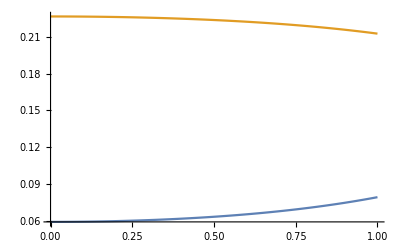

```mathematica
Plot[{ga[r]/.sol/.bsol/.gabBsol/.{k1x->4,km1x->1,k1->1,km1->1,pAinf->0.1},gb[r]/.sol/.bsol/.gabBsol/.{k1x->4,km1x->1,k1->2,km1->1,pAinf->0.1}},{r,0,1}]
```

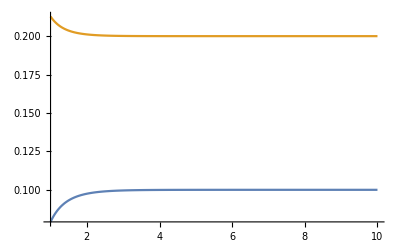

```mathematica
Plot[{pA0[r]/.bsol/.gabBsol/.{k1x->4,km1x->1,k1->1,km1->1,pAinf->0.1},pB0[r]/.bsol/.gabBsol/.{k1x->4,km1x->1,k1->2,km1->1,pAinf->0.1}},{r,1,10}]
```

```mathematica
ga0=Limit[ga[r]/.sol,r->0]/.bsol/.gabBsol//FullSimplify
```

(ⅇ^(-2 √(k1x+km1x)) (1+√(k1+km1)) (2 ⅇ^(2 √(k1x+km1x)) (k1+km1) (1+√(k1+km1)) km1x (-k1+k1x-km1+km1x)+2 ⅇ^(√(k1x+km1x)) (k1x km1-k1 km1x) (k1x (1+k1+km1+2 √(k1+km1))+(1+k1+km1+2 √(k1+km1)) km1x-(√(k1+km1)+k1 (2+√(k1+km1))+km1 (2+√(k1+km1))) √(k1x+km1x))+2 ⅇ^(3 √(k1x+km1x)) (k1x km1-k1 km1x) (k1x (1+k1+km1+2 √(k1+km1))+(1+k1+km1+2 √(k1+km1)) km1x+(√(k1+km1)+k1 (2+√(k1+km1))+km1 (2+√(k1+km1))) √(k1x+km1x))+(k1+km1) km1x (k1x+km1+k1x √(k1+km1)+km1 √(k1+km1)+km1x+√(k1+km1) km1x-2 km1 √(k1x+km1x)-2 √(k1+km1) √(k1x+km1x)+k1 (1+√(k1+km1)-2 √(k1x+km1x)))+ⅇ^(4 √(k1x+km1x)) (k1+km1) km1x (k1x+km1+k1x √(k1+km1)+km1 √(k1+km1)+km1x+√(k1+km1) km1x+2 km1 √(k1x+km1x)+2 √(k1+km1) √(k1x+km1x)+k1 (1+√(k1+km1)+2 √(k1x+km1x)))) pAinf)/(4 km1 (k1x+km1x) ((1+√(k1+km1)) √(k1x+km1x) Cosh[√(k1x+km1x)]+(k1+km1+√(k1+km1)) Sinh[√(k1x+km1x)])^2)

```mathematica
gb0=Limit[gb[r]/.sol,r->0]/.bsol/.gabBsol//FullSimplify
```

(ⅇ^(√(k1x+km1x)-((k1x+km1x)^(3/2))^(1/3)) (1+√(k1+km1)) pAinf ((1+√(k1+km1)) (k1x+km1x) (-k1x km1+k1 km1x)+k1x (k1+km1) (k1x+km1x) Cosh[√(k1x+km1x)]+k1x (k1+km1)^(3/2) √(k1x+km1x) Sinh[√(k1x+km1x)]))/(km1 (1+√(k1+km1)) (k1x+km1x)^2 Cosh[√(k1x+km1x)]+km1 (k1+km1+√(k1+km1)) (k1x+km1x)^(3/2) Sinh[√(k1x+km1x)])

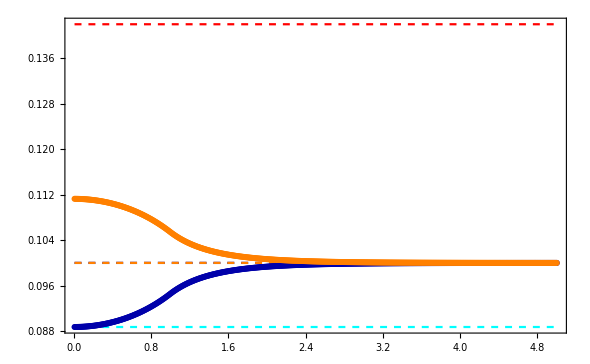

```mathematica
Show[ListPlot[Table[If[r<1,{r,ga[r]/.sol/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}},{r,pA0[r]/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}}],{r,0.01,5,0.01}],PlotStyle->Darker[Blue]],
ListPlot[Table[If[r<1,{r,gb[r]/.sol/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}},{r,pB0[r]/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}}],{r,0.01,5,0.01}],PlotStyle->Orange],ListPlot[Table[{r,0.1},{r,0.01,5,0.01}],Joined->True,PlotStyle->{Darker[Blue],Dashed}],ListPlot[Table[{r,0.1},{r,0.01,5,0.01}],Joined->True,PlotStyle->{Orange,Dashed}],ListPlot[Table[{r,ga0/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}},{r,0.01,5,0.01}],Joined->True,PlotStyle->{Cyan,Dashed}],ListPlot[Table[{r,ga0 k1x/km1x/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}},{r,0.01,5,0.01}],Joined->True,PlotStyle->{Red,Dashed}],PlotRange->All,Frame->True]
```

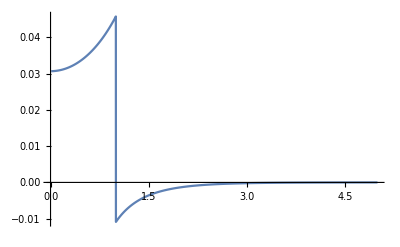

```mathematica
ListPlot[Table[{r,If[r<1,(k1x ga[r]-km1x gb[r])/.sol/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(k1 pA0[r]-km1 pB0[r])/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}]},{r,0.01,5,0.001}],PlotRange->All,Joined->True]
```

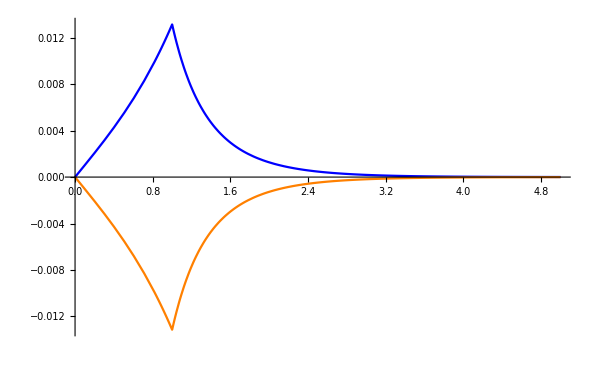

```mathematica
Show[Plot[If[rr<1,(D[ga[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(D[pA0[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}],{rr,0,5},PlotStyle->Blue],
Plot[If[rr<1,(D[gb[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(D[pB0[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}],{rr,0,5},PlotStyle->Orange],PlotRange->All]
```

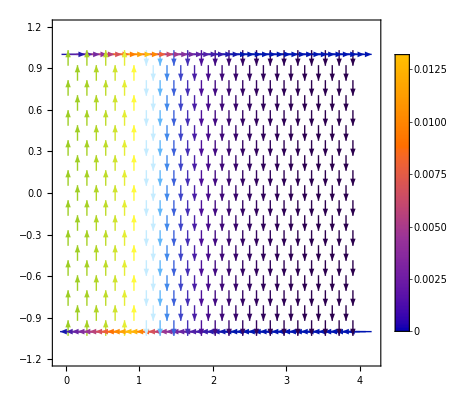

```mathematica
Show[VectorPlot[{If[rr<1,(D[ga[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(D[pA0[r]/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}],0},{rr,-0.1,4.2},{y,-1.2,1.2},VectorPoints->Table[{x,1},{x,0,4,0.1}],PlotLegends->Automatic],VectorPlot[{If[rr<1,(D[gb[r]/.sol/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},(D[pB0[r]/.bsol/.gabBsol,r])/.r->rr/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}],0},{rr,-0.1,4.2},{y,-1.2,1.2},VectorPoints->Table[{x,-1},{x,0,4,0.08}],PlotLegends->Automatic],VectorPlot[{0,If[r<1,(k1x ga[r]-km1x gb[r])/.sol/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1},0]},{r,-0.1,4},{y,-1,1},VectorColorFunction->"AvocadoColors",PlotLegends->Automatic],VectorPlot[{0,If[r<1,0,(k1 pA0[r]-km1 pB0[r])/.bsol/.gabBsol/.{k1x->1.6,km1x->1,k1->1,km1->1,pAinf->0.1}]},{r,1,4},{y,-1,1},VectorColorFunction->"DeepSeaColors",PlotLegends->Automatic]]
```

## Section 4 - 3-state solution with sharp interface - The solution coincides with Section 1

```mathematica
kAB=Exp[-VB+epsAB];
kBA=Exp[-VA+epsAB];
kAC=Exp[-VC+epsAC];
kCA=Exp[-VA+epsAC];
kBC=Exp[-VC+epsBC];
kCB=Exp[-VB+epsBC];
```

```mathematica
kABaf=Exp[-VBaf+epsAB];
kBAaf=Exp[-VAaf+epsAB];
kACaf=Exp[-VCaf+epsAC];
kCAaf=Exp[-VAaf+epsAC];
kBCaf=Exp[-VCaf+epsBC];
kCBaf=Exp[-VBaf+epsBC];
```

```mathematica
epsAB=1;
epsAC=1;
epsBC=1;
```

```mathematica
VA=0;
VB=0;
VC=0;
VAaf=1;
VBaf=1.3;
VCaf=2;
```

```mathematica
l=2;
in=1;
norm=1;
```

```mathematica
solBEFORE=Flatten[DSolve[{-kAB pA[x]+kBA pB[x]-kAC pA[x]+kCA pC[x]+D[pA[x],{x,2}]==0,kAB pA[x]-kBA pB[x]+kCB pC[x]-kBC pB[x]+D[pB[x],{x,2}]==0,kAC pA[x]-kCA pC[x]+kBC pB[x]-kCB pC[x]+D[pC[x],{x,2}]==0,pA'[0]==0,pB'[0]==0,pC'[0]==0,pA[in]==gA,pB[in]==gB,pC[in]==norm-gA-gB},{pA[x],pB[x],pC[x]},{x,0,in}]]//FullSimplify
```

{pA[x]→(ⅇ^(-√(3 ⅇ) x) (ⅇ^(√(3 ⅇ) x)+ⅇ^(√(3 ⅇ) (2+x))+ⅇ^(√(3 ⅇ)) (-1+3 gA)+ⅇ^(√(3 ⅇ) (1+2 x)) (-1+3 gA)))/(3 (1+ⅇ^(2 √(3 ⅇ)))),pB[x]→(ⅇ^(-√(3 ⅇ) x) (ⅇ^(√(3 ⅇ) x)+ⅇ^(√(3 ⅇ) (2+x))+ⅇ^(√(3 ⅇ)) (-1+3 gB)+ⅇ^(√(3 ⅇ) (1+2 x)) (-1+3 gB)))/(3 (1+ⅇ^(2 √(3 ⅇ)))),pC[x]→(ⅇ^(-√(3 ⅇ) x) (ⅇ^(√(3 ⅇ) x)+ⅇ^(√(3 ⅇ) (2+x))+ⅇ^(√(3 ⅇ)) (2-3 gA-3 gB)+ⅇ^(√(3 ⅇ) (1+2 x)) (2-3 gA-3 gB)))/(3 (1+ⅇ^(2 √(3 ⅇ))))}

```mathematica
solAFTER=Flatten[DSolve[{-kABaf pA[x]+kBAaf pB[x]-kACaf pA[x]+kCAaf pC[x]+D[pA[x],{x,2}]==0,kABaf pA[x]-kBAaf pB[x]+kCBaf pC[x]-kBCaf pB[x]+D[pB[x],{x,2}]==0,kACaf pA[x]-kCAaf pC[x]+kBCaf pB[x]-kCBaf pC[x]+D[pC[x],{x,2}]==0,pA'[l]==0,pB'[l]==0,pC'[l]==0,pA[in]==gA,pB[in]==gB,pC[in]==norm-gA-gB},{pA[x],pB[x],pC[x]},{x,in,l}]]//FullSimplify//Chop
```

{pA[x]→0.474226+ⅇ^(1.45214 x) (-0.00576576+0.0121583 gA)+ⅇ^(-1.45214 x) (0.63042-0.298107 gA-1.39205 gB)+ⅇ^(-1.45214 x) (-2.55119+4.34842 gA+1.39205 gB),pB[x]→0.351316+ⅇ^(-1.45214 x) (0.546335-0.931212 gA-0.298107 gB)+ⅇ^(1.45214 x) (-0.00427138+0.0121583 gB)+ⅇ^(-1.45214 x) (-1.96927+0.931212 gA+4.34842 gB),pC[x]→0.174458+ⅇ^(-1.45214 x) (1.33885-0.633105 gA-2.95637 gB)+ⅇ^(-1.45214 x) (2.00485-3.41721 gA-1.09395 gB)+ⅇ^(1.45214 x) (0.0100371-0.0121583 gA-0.0121583 gB)}

```mathematica
pBEFORE={pA[x],pB[x],pC[x]}/.solBEFORE;
pAFTER={pA[x],pB[x],pC[x]}/.solAFTER;
```

```mathematica
gsolINT={gA,gB}/.Flatten[Solve[{(D[pBEFORE[[1]],x]/.x->in)==(D[pAFTER[[1]],x]/.x->in),(D[pBEFORE[[2]],x]/.x->in)==(D[pAFTER[[2]],x]/.x->in)},{gA,gB}]]
```

{0.377639,0.338988}

```mathematica
gAn=gsolINT[[1]];
gBn=gsolINT[[2]];
gsol={gA->gAn,gB->gBn,gC->norm-gAn-gBn};
```

```mathematica
en={1HeavisideTheta[x-in],1.3HeavisideTheta[x-in],2HeavisideTheta[x-in]};
kvec=Table[Exp[-en[[j]]+1] 1,{i,1,nn},{j,1,nn}];
For[i=1,i≤nn,i++,
kvec[[i,i]]=0;
];
kvec[[1,2]]=kvec[[1,2]];
```

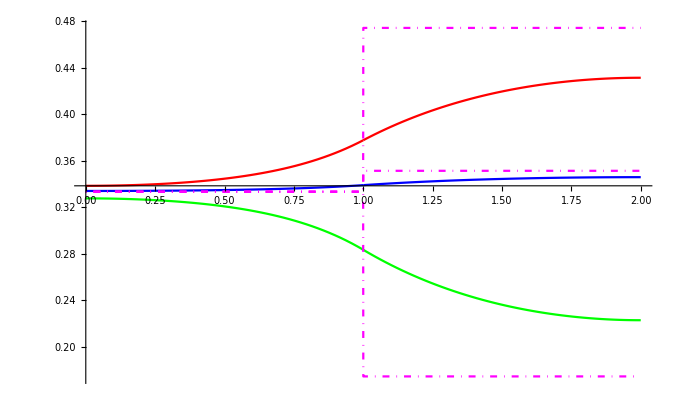

```mathematica
Show[Plot[pBEFORE[[1]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Red],Plot[pAFTER[[1]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Red],Plot[pBEFORE[[2]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Blue],Plot[pAFTER[[2]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Blue],Plot[pBEFORE[[3]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Green],Plot[pAFTER[[3]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Green],Plot[{((kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm,((kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm,((kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm},{x,0,l},PlotStyle->{{DotDashed,Magenta},{DotDashed,Magenta},{DotDashed,Magenta}},PlotRange->All]]
```

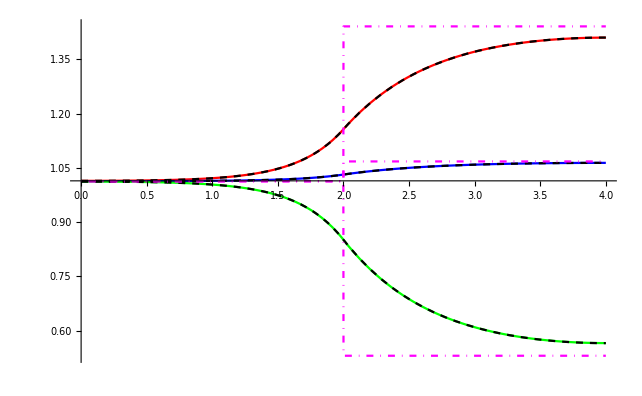

```mathematica
Show[Plot[pBEFORE[[1]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Red],Plot[pAFTER[[1]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Red],Plot[pBEFORE[[2]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Blue],Plot[pAFTER[[2]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Blue],Plot[pBEFORE[[3]]/.gsol,{x,0,in},PlotRange->All,PlotStyle->Green],Plot[pAFTER[[3]]/.gsol,{x,in,l},PlotRange->All,PlotStyle->Green],Plot[{psoleq[[1]][x],psoleq[[2]][x],psoleq[[3]][x],((kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm,((kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm,((kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) norm},{x,0,4},PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{DotDashed,Magenta},{DotDashed,Magenta},{DotDashed,Magenta}}],PlotRange->All]
```

{{ⅇ^(1-HeavisideTheta[-2+x]),ⅇ^(1-1.3 HeavisideTheta[-2+x]),ⅇ^(1-2 HeavisideTheta[-2+x])},{ⅇ^(1-HeavisideTheta[-2+x]),ⅇ^(1-1.3 HeavisideTheta[-2+x]),ⅇ^(1-2 HeavisideTheta[-2+x])},{ⅇ^(1-HeavisideTheta[-2+x]),ⅇ^(1-1.3 HeavisideTheta[-2+x]),ⅇ^(1-2 HeavisideTheta[-2+x])}}

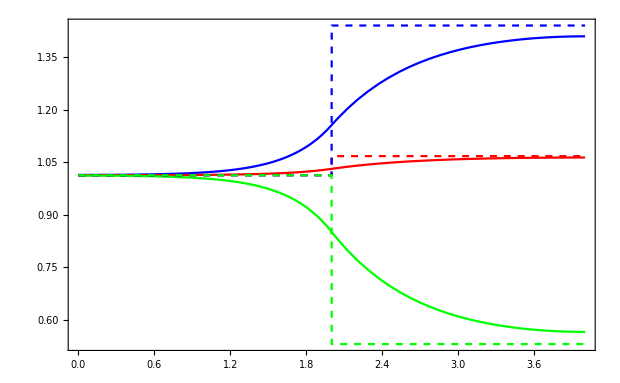

```mathematica
en={1HeavisideTheta[x-in],1.3HeavisideTheta[x-in],2HeavisideTheta[x-in]};
kvec=Table[Exp[-en[[j]]+1] 1,{i,1,nn},{j,1,nn}]
For[i=1,i≤nn,i++,
kvec[[i,i]]=0;
];
sys=Quiet[Table[Sum[kvec[[j,i]] p[[j]][x]-kvec[[i,j]] p[[i]][x]+KroneckerDelta[j,i] D[p[[i]][x],{x,2}],{j,1,nn}]==0,{i,1,nn}]];
psoleq=Quiet[Table[p[[i]],{i,1,nn}]]/.Quiet[Flatten[NDSolve[Flatten[Join[sys,Table[p[[i]]'[0]==0,{i,1,nn}],Table[p[[i]]'[l]==0,{i,1,nn}]]],Table[p[[i]],{i,1,nn}],{x,0,l}]]];
ptoteq[xx_]:=Sum[psoleq[[i]][xx],{i,1,nn}];
Plot[{psoleq[[1]][x],psoleq[[2]][x],psoleq[[3]][x],((kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x],((kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x],((kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])/(kvec[[1,2]] kvec[[3,2]]+kvec[[1,3]] kvec[[3,2]]+kvec[[3,1]] kvec[[1,2]]+kvec[[2,1]] kvec[[3,1]]+kvec[[2,3]] kvec[[3,1]]+kvec[[3,2]] kvec[[2,1]]+kvec[[1,3]]kvec[[2,3]]+kvec[[1,2]]kvec[[2,3]]+kvec[[2,1]]kvec[[1,3]])) ptoteq[x]},{x,0,4},PlotStyle->{Blue,Red,Green,{Red,Dashed},{Blue,Dashed},{Green,Dashed}},PlotRange->All,Frame->True]
```

```mathematica
ptoteq[0]
```

3.03953